## General Second-Order Runge-Kutta — Damped Oscillator

## Done in class, January 31, 2025

This is the fourth notebook for you to finish in-class.

### Damped Oscillator

#### Problem Description

```mathematica
springForce[x_, v_]:=-20 x-2v
mass=5;
a[x_, v_] := springForce[x,v]/mass;
tInitial = 0;
tFinal = 5Pi; 
steps = 1200;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Conditions

Let’s stretch this spring to x_initial=25 and let it go with no initial velocity, so v_initial=0.0.

```mathematica
xInitial=25.0;
vInitial=0.0;
initialConditions={tInitial,xInitial,vInitial};
```

#### General Second-Order Runge-Kutta — Theory — Summary

This is a more general version of Second-Order Runge-Kutta, which has a parameter α, typically chosen as α=1/2 or α=1:

t^*=t+αΔt

x^*=x(t_i)+v(t_i)·αΔt

v^*=v(t_i)+a(t_i,x(t_i),v(t_i))·αΔt

t_(i+1)=t_i+Δt

v(t_(i+1))=v(t_i)+((1-1/(2α))a(t_i,x(t_i),v(t_i))+1/(2α)a(t^*,x^*,v^*))·Δt

x(t_(i+1))=x(t_i)+ (v(t_i)+v(t_(i+1)))Δt/2

#### General Second-Order Runge-Kutta — Implementation

```mathematica
alpha=1;
rungeKutta2[cc_]:=(
(* Extract time, position, and velocity from the list. *)
curTime=cc[[1]];
curPosition = cc[[2]];
curVelocity=cc[[3]];
(* Implement the six equations in the theory above. *)
tStar=curTime+alpha deltaT;
xStar=curPosition+curVelocity alpha deltaT;
vStar=curVelocity+a[curPosition, curVelocity]alpha deltaT;
newTime=curTime+deltaT;
newVelocity=curVelocity+((1-1/(2alpha))a[curPosition,curVelocity]+1/(2alpha)a[xStar,vStar])deltaT;
newPosition=curPosition+(curVelocity+newVelocity)deltaT/2;
{newTime, newPosition, newVelocity}
)
```

#### Displaying Damped Oscillation

Nest the procedure and then transpose the results to produce position and velocity plots:

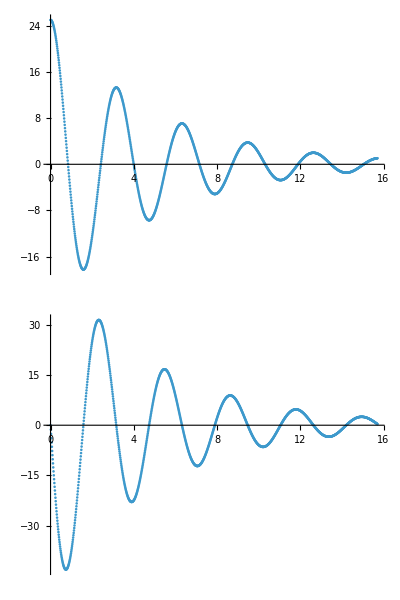

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
positionPlot = ListPlot[Transpose[rk2ResultsTransposed[[{1,2}]]]];
velocityPlot = ListPlot[Transpose[rk2ResultsTransposed[[{1,3}]]]];
Column[{positionPlot, velocityPlot}]
```

```mathematica
positions=rk2ResultsTransposed[[2]];
```

```mathematica
Animate[NumberLinePlot[positions[[step]],PlotRange->{-25,25}],{step, 0, steps, 1}]
```

#### Conclusion / Commentary

Our oscillator now has the force law F(x)=-20x-2v. Nowhere did we put sines or cosines or decaying exponential functions into the problem! Damped oscillation (for which the position is the product of a cosine and a decaying exponential) has emerged from the force law and from our implementation of numerical methods.